Supplementary code for: Bert Wuyts, Jan Sieber, “Automated derivation of moment closures for multistate dynamics on networks” [in review with PRE]. https://arxiv.org/abs/2111.07643

# Moment closure for SIS spreading on the square lattice (4th order)

Bert Wuyts

Centre for Systems, Dynamics and Control, University of Exeter, United Kingdom

email: b3rtwu@gmail.com

In this notebook, we obtain the mean-field approximation of SIS epidemic spreading on the square lattice. We do this by first deriving moment equations and then closing these equations via a closure approximation. We exploit conservation relations such that fewer equations need to be derived. This is a demo of our package for moment closure for dynamics on networks.

Load package

```mathematica
<<mfmcl`
```

Define the dynamical process: SIS spreading

The process is defined by its state space on nodes (l)  and its conversion rates (R0: spontaneous, R1: nearest-neighbour induced). R0[[i,j]] is the rate at which l[[i]] spontaneously converts to l[[j]]. R1[[i,j,k]] is the rate at which l[[i]]  converts to l[[j]] for each link to l[[k]]. For SIS spreading this is:

```mathematica
l={{"S",RGBColor[0.32, 0.65, 1]},{"I",RGBColor[1, 0.56, 0.11]}};n=Length[l]; (*state labels*)
R0={{0,0},{γ,0}}; (*I->S at rate γ*)
R1=ConstantArray[0,{n,n,n}]; 
R1[[All,All,2]]={{0,β},{0,0}};(*I<->S->I<->I at rate β*)
sisprocess={l,R0,R1};
```

Obtain the frequencies of induced subgraphs in the square lattice

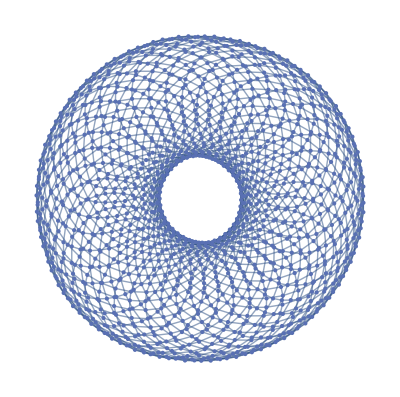

```mathematica
L=40;
Gsql=ResourceFunction["TorusGraph"][{L,L}](*40 by 40 square lattice with periodic boundaries*)
```

Choose truncation order for the moment equation system in the next section (= max motif size)

```mathematica
k=4;
```

Enumerate  all possible subgraphs up to k+1






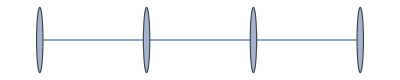
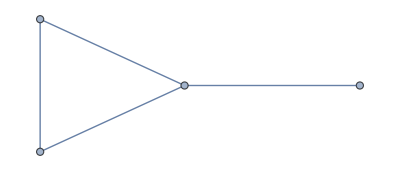
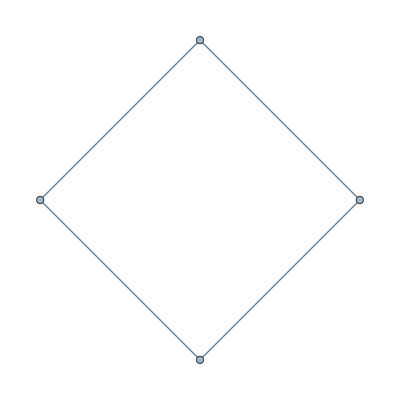
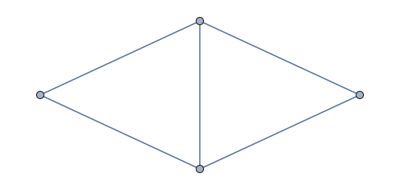
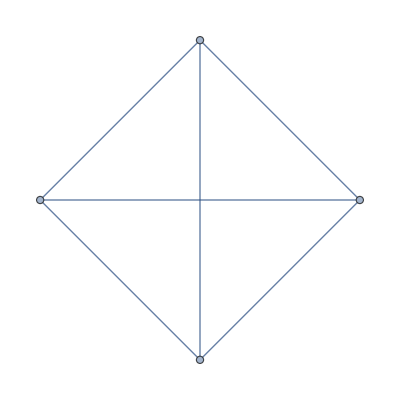
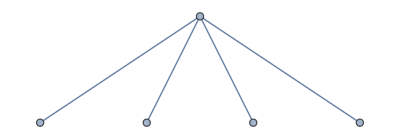
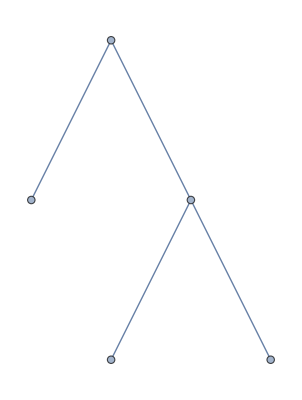
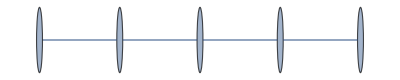

```mathematica
gskp1=enumerateGraphs/@Range[k+1]
```

Count these for the square lattice (relative to N=L^2)

```mathematica
counts=(countInducedSubgraphs[#,Gsql]&/@Flatten[gskp1])/L^2
```

{1,4,12,0,24,28,0,8,0,0,24,40,68,0,0,0,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Construct list with subgraph types and counts to be used in the next section

```mathematica
gfreqs=Select[Transpose[{Flatten[gskp1]}~Join~{counts}],#[[2]]!=0&]
```

{{-Graphics-,1},{-Graphics-,4},{-Graphics-,12},{-Graphics-,24},{-Graphics-,28},{-Graphics-,8},{-Graphics-,24},{-Graphics-,40},{-Graphics-,68},{-Graphics-,16}}

Obtain moment equations

Select the induced subgraphs up to k:

```mathematica
gs=Select[Flatten@gfreqs[[;;,1]],VertexCount[#]<=k&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Find all motifs (induced subgraphs labelled with states):

```mathematica
mots=(enumerateMotifs[#,l]&/@gs)//Flatten
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Find indices of dynamically irrelevant motifs (those with no infected states). In the paper, we remove these from the list of variables to keep but here we will add them to the list of to be eliminated variables instead.

```mathematica
nI=Count[AnnotationValue[#,VertexLabels][[;;,2,1]],l[[2,1]]]&;
pnI0=Position[nI/@mots,0]
```

{{1},{3},{6},{12},{20},{30}}

Set up (normalised) conservation equations to decide which motifs to derive equations for

```mathematica
(cons=consEqs[gs,l,MotifList->mots,HomogeneousDegree->True])//TableForm
```

⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==⟨-Graphics-⟩
⟨-Graphics-⟩+⟨-Graphics-⟩==1
⟨-Graphics-⟩+4 ⟨-Graphics-⟩+4 ⟨-Graphics-⟩+2 ⟨-Graphics-⟩+4 ⟨-Graphics-⟩+⟨-Graphics-⟩==1

```mathematica
{{Qp,c},x,xkp1}=getMomentEqs[gs,mots,sisprocess,SubgraphFrequencies->gfreqs,ElimViaConsEqs->True,posDynamicIrrelevantMotifs->Flatten@pnI0,ConsEqs->cons,OutputFormat->"Matrix"];
```

Show respectively: moment equation matrix, constant term, motifs that have been kept, and, highest-order motifs. (Note that in the paper, x and x_(k+1) have tildes to indicate that some motifs were omitted via conservation equations.)

```mathematica
Qp//MatrixForm
c
x
xkp1
```

(-γ | 4 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γ | -2 (2 β+γ) | 0 | 6 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 γ | -3 γ-20/3 β | 0 | 0 | 2 β | 14/3 β | 0 | 0 | 0 | 0 | -4/3 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 γ | -γ | -2/3 (8 β+3 γ) | 0 | 2 β | 0 | 0 | 14/3 β | 2/3 β | -2/3 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 γ | 0 | -3 β-4 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 β | β | -5 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | γ | 2 γ | -γ | -β-3 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/3 β | -β | 5/3 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/3 β | 0 | -10/3 β | 0 | 0 | 0 | 0 | -4/3 β | 0 | 0 | 0
0 | 0 | γ | γ | 0 | 0 | -2 β-3 γ | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4/7 β | 10/7 β | -17/7 β | -17/7 β | -8/7 β | 0 | -10/7 β | 0 | 4/7 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 γ | -2 γ | 0 | 0 | 0 | 2 β | -2 (β+2 γ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8/7 β | -8/7 β | 20/7 β | -34/7 β | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | γ | 2 γ | 0 | 0 | -2 γ | 0 | -β-2 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4/7 β | -4/7 β | -10/7 β | -10/7 β | 17/7 β | -17/7 β | 0 | -8/7 β | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 β-γ | 2 γ | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 β | -4 β | -2 β | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 β | -2 (β+γ) | 0 | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 β | 0 | 0 | -4 β | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 (2 β+γ) | 2 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 β | -4 β | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 β | 2 β | -2 β-3 γ | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 β | 4 β | -2 β
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 β | -4 γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 8 β)

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩}

{⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩,⟨-Graphics-⟩}

Show in table form (c=0, so no need to show constant term)

```mathematica
x1kp1=x~Join~xkp1;
coeffTab[Qp,x1kp1,True]
```

⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩
-γ | 4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
γ | -2 (2 β+γ) | . | 6 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | 2 γ | -3 γ-20/3 β | . | . | 2 β | 14/3 β | . | . | . | . | -4/3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | 2 γ | -γ | -2/3 (8 β+3 γ) | . | 2 β | . | . | 14/3 β | 2/3 β | -2/3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | 3 γ | . | -3 β-4 γ | . | . | . | . | . | . | . | . | . | -4 β | β | -5 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | γ | 2 γ | -γ | -β-3 γ | . | . | . | . | . | . | . | . | . | . | . | 4/3 β | -β | 5/3 β | . | . | . | . | . | . | . | . | . | -4/3 β | . | -10/3 β | . | . | . | . | -4/3 β | . | . | .
. | . | γ | γ | . | . | -2 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | -4/7 β | 10/7 β | -17/7 β | -17/7 β | -8/7 β | . | -10/7 β | . | 4/7 β | . | . | . | . | . | . | . | . | . | . | .
. | 2 γ | -2 γ | . | . | . | 2 β | -2 (β+2 γ) | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8/7 β | -8/7 β | 20/7 β | -34/7 β | . | . | . | . | . | . | . | . | . | . | . | .
. | . | γ | 2 γ | . | . | -2 γ | . | -β-2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4/7 β | -4/7 β | -10/7 β | -10/7 β | 17/7 β | -17/7 β | . | -8/7 β | . | . | . | .
. | . | . | . | . | . | . | . | . | -2 β-γ | 2 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | -4 β | -2 β | . | . | .
. | . | . | . | . | . | . | . | . | 2 β | -2 (β+γ) | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | . | -4 β | .
. | . | . | . | . | . | . | . | . | . | . | -2 (2 β+γ) | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | -4 β | . | .
. | . | . | . | . | . | . | . | . | . | 2 β | 2 β | -2 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 4 β | -2 β
. | . | . | . | . | . | . | . | . | . | . | . | 8 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 β

Show in equation form:

```mathematica
dxdto=Qp.x1kp1+c;
TraditionalForm@TableForm@MapThread[d/dt#1==#2&,{x,dxdto}]
```

(d ⟨-Graphics-⟩)/dt==4 β ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩-2 (2 β+γ) ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-20/3 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4/3 β ⟨-Graphics-⟩+14/3 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2/3 (8 β+3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2/3 β ⟨-Graphics-⟩+2/3 β ⟨-Graphics-⟩+14/3 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-4 γ) ⟨-Graphics-⟩-5 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+3 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-3 γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩-4/3 β ⟨-Graphics-⟩-4/3 β ⟨-Graphics-⟩+4/3 β ⟨-Graphics-⟩+5/3 β ⟨-Graphics-⟩-10/3 β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-3 γ) ⟨-Graphics-⟩-4/7 β ⟨-Graphics-⟩+4/7 β ⟨-Graphics-⟩-8/7 β ⟨-Graphics-⟩-10/7 β ⟨-Graphics-⟩+10/7 β ⟨-Graphics-⟩-17/7 β ⟨-Graphics-⟩-17/7 β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 (β+2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-8/7 β ⟨-Graphics-⟩+8/7 β ⟨-Graphics-⟩+20/7 β ⟨-Graphics-⟩-34/7 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-2 γ) ⟨-Graphics-⟩-4/7 β ⟨-Graphics-⟩+4/7 β ⟨-Graphics-⟩-8/7 β ⟨-Graphics-⟩-10/7 β ⟨-Graphics-⟩-10/7 β ⟨-Graphics-⟩-17/7 β ⟨-Graphics-⟩+17/7 β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 (β+γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 (2 β+γ) ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+8 β ⟨-Graphics-⟩+8 β ⟨-Graphics-⟩

Close moment equations

Apply the closure formula to the largest motifs (here using the junction tree algorithm for chordal graphs and ad-hoc formula for complete graphs and loops (here referred to as generalised Kirkwood)):

```mathematica
motskeep=x/.⟨x_Graph⟩:>x;motsh=xkp1/.⟨x_Graph⟩:>x;(*remove brackets*)
```

```mathematica
replh=closeJT[#,l,methodlc->"kirkwood"]&/@motsh;
(replh=replIsom[replh,l,Flatten[gs],mots])//TableForm (*make sure isomorphic motifs have the same indexing*)
```

⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩^3)/⟨-Graphics-⟩^3
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩^2 ⟨-Graphics-⟩^2)/⟨-Graphics-⟩^3
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→⟨-Graphics-⟩^2/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩

Substitute from the closure formulas motifs that we chose to eliminate

```mathematica
solcons=Solve[cons,⟨#⟩&/@Complement[mots,motskeep]][[1]];
(replh=(replh/.solcons))//TableForm
```

⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→((1-⟨-Graphics-⟩-⟨-Graphics-⟩)^3 ⟨-Graphics-⟩)/(1-⟨-Graphics-⟩)^3
⟨-Graphics-⟩→((⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→((1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((1-⟨-Graphics-⟩-⟨-Graphics-⟩)^2 ⟨-Graphics-⟩^2)/(1-⟨-Graphics-⟩)^3
⟨-Graphics-⟩→(⟨-Graphics-⟩ (1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩))/(1-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(1-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ (⟨-Graphics-⟩-⟨-Graphics-⟩))/⟨-Graphics-⟩
⟨-Graphics-⟩→((⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩)
⟨-Graphics-⟩→(⟨-Graphics-⟩ (⟨-Graphics-⟩-⟨-Graphics-⟩))/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ (⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+⟨-Graphics-⟩))/(⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→((1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩) (⟨-Graphics-⟩-⟨-Graphics-⟩))/(1-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/(1-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→⟨-Graphics-⟩^2/(1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→(⟨-Graphics-⟩ (1-⟨-Graphics-⟩-4 ⟨-Graphics-⟩-4 ⟨-Graphics-⟩-2 ⟨-Graphics-⟩-4 ⟨-Graphics-⟩))/(1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→(⟨-Graphics-⟩ ⟨-Graphics-⟩)/(1-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)
⟨-Graphics-⟩→((⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩
⟨-Graphics-⟩→((⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)

Show final system of closed equations:

```mathematica
dxdtc=dxdto/.replh;
TraditionalForm@TableForm@MapThread[d/dt#1==#2&,{x,dxdtc}]
```

(d ⟨-Graphics-⟩)/dt==4 β ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩-2 (2 β+γ) ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-20/3 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4/3 β ⟨-Graphics-⟩+14/3 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2/3 (8 β+3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2/3 β ⟨-Graphics-⟩+2/3 β ⟨-Graphics-⟩+14/3 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-4 γ) ⟨-Graphics-⟩+(β ⟨-Graphics-⟩ (-⟨-Graphics-⟩-⟨-Graphics-⟩+1)^3)/(1-⟨-Graphics-⟩)^3-(5 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩-(4 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩+3 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-3 γ) ⟨-Graphics-⟩-(β (-⟨-Graphics-⟩-⟨-Graphics-⟩+1)^2 ⟨-Graphics-⟩^2)/(1-⟨-Graphics-⟩)^3-(4/3 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩+(4/3 β (-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1) ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)-(4/3 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)+(5/3 β ⟨-Graphics-⟩ (-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1))/(-⟨-Graphics-⟩-⟨-Graphics-⟩+1)-(10/3 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩+1)+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-3 γ) ⟨-Graphics-⟩-(10/7 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩-(4/7 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)+(4/7 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩-(8/7 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)+(10/7 β (-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1) ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩+1)-(17/7 β ⟨-Graphics-⟩ (⟨-Graphics-⟩-⟨-Graphics-⟩))/⟨-Graphics-⟩-(17/7 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 (β+2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-(8/7 β (⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(-2 ⟨-Graphics-⟩+⟨-Graphics-⟩+⟨-Graphics-⟩)+(8/7 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)-(34/7 β ⟨-Graphics-⟩ (⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+⟨-Graphics-⟩))/(⟨-Graphics-⟩-⟨-Graphics-⟩)+(20/7 β ⟨-Graphics-⟩ (⟨-Graphics-⟩-⟨-Graphics-⟩))/⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-2 γ) ⟨-Graphics-⟩-(17/7 β ⟨-Graphics-⟩^2)/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)+(17/7 β (-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1) ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)-(4/7 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩+(4/7 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/⟨-Graphics-⟩-(8/7 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩-(10/7 β (-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1) (⟨-Graphics-⟩-⟨-Graphics-⟩))/(-⟨-Graphics-⟩-⟨-Graphics-⟩+1)-(10/7 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩+1)+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩-2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩+(2 β ⟨-Graphics-⟩ (-4 ⟨-Graphics-⟩-4 ⟨-Graphics-⟩-2 ⟨-Graphics-⟩-4 ⟨-Graphics-⟩-⟨-Graphics-⟩+1))/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)-(4 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩-(2 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 (β+γ) ⟨-Graphics-⟩-(4 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+(4 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 (2 β+γ) ⟨-Graphics-⟩-(4 β (⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)+(4 β ⟨-Graphics-⟩ ⟨-Graphics-⟩)/(-⟨-Graphics-⟩-⟨-Graphics-⟩-⟨-Graphics-⟩+1)+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-3 γ) ⟨-Graphics-⟩-(2 β (⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)+2 β ⟨-Graphics-⟩+(4 β (⟨-Graphics-⟩-⟨-Graphics-⟩) ⟨-Graphics-⟩)/⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+(2 β (⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+8 β ⟨-Graphics-⟩+(8 β (⟨-Graphics-⟩-2 ⟨-Graphics-⟩+⟨-Graphics-⟩) ⟨-Graphics-⟩)/(⟨-Graphics-⟩-⟨-Graphics-⟩)

Export to MATLAB

One can continue to work with these equations in Mathematica but this becomes inefficient for higher orders. Here, we show how to export the mean-field equations to MATLAB functions. These functions can be used for numerical integration in MATLAB, or one can use the numerical continuation packages to obtain the steady states. The output (xdot) is written in a format compatible with Coco or Matcont.

First replace Greek characters (which would otherwise be parsed incorrectly):

```mathematica
dxdtcf=dxdtc/.{β -> beta, γ -> gamma};
```

Arguments for output:

```mathematica
outdir=NotebookDirectory[];
filename="SISMF4";
parameters={beta,gamma};
$RecursionLimit=Infinity;
```

Write output:

```mathematica
exportMF[outdir,filename,dxdtcf,x,{beta,gamma},MatcontOrCoco->"coco"]
```